## Dengue 7-1-7 analysis — Thailand (2016–2024)

Author: Sompob Saralamba

Affiliation: Mahidol Oxford Tropical Medicine Research Unit (MORU)

Contact: sompob@tropmedres.ac

This notebook reproduces analyses in : "How much could faster outbreak response reduce dengue burden? 
A 7-1-7–inspired analysis using national surveillance data from Thailand."

### Overview

This notebook implements the data cleaning, outbreak detection, counterfactual scenario analyses, and bootstrap uncertainty quantification used in the manuscript . 
Outputs include :

weekly threshold plot used to identify outbreaks (Figure 2)

sensitivity plot of median cases averted vs weeks shortened (Figure 3)

supplementary tables of outbreak - specific counterfactual estimates

```mathematica
(*Record session info*)
$VersionNumber
$OperatingSystem
DateString[]
```

14.3

Windows

Thu 19 Mar 2026 21:38:00

### Data Input

The example of the data format.

```mathematica
data=Import["YOURDATA.CSV","Dataset"];
```

```mathematica
(*the data for this study*)
data=;
```

```mathematica
byYW=Query[GroupBy[#year&],GroupBy[#week&],All,#cases&][data];
```

```mathematica
q={0.70,0.75,0.80,0.85,0.90};
baselineByWeek=Query[GroupBy[#week&],Median,#cases&][data];
thresholdByWeek=Table[Query[GroupBy[#week&],Quantile[#,j]&,#cases&][data],{j,q}];
```

```mathematica
ab80=Map[Function[r,With[{w=r["week"]},Join[r,<|"baseline"->baselineByWeek[w],"threshold"->thresholdByWeek[[3]][w],"above"->(r["cases"]>thresholdByWeek[[3]][w])|>]]],data];
```

```mathematica
(* find the positions that the dengue cases were above the threshold (at 80%)*)
FindOutBreak[Y_]:=Module[{trsh,atyr},
trsh=Select[Normal@Select[ab80,#year==Y&][All,{#week,#cases,#above}&],#[[3]]==True&][[All,{1,2}]];
atyr=Select[ab80,#year==Y&][All,{#week,#cases}&];
If[trsh!={},
ListPlot[{thresholdByWeek[[2]],atyr,trsh},
Joined->{True, True,False},PlotStyle->{Automatic,Automatic,{Red,PointSize[0.02]}},
PlotRange->{{0,55},{0,8000}},Frame->True,GridLines->Automatic,FrameLabel->{"Week", "Cases"},PlotLegends->Placed[{"threshold at 80%","data at "<>ToString[Y],"Outbreak"}, Below],PlotLabel->Y,ImageSize->Medium]
,
ListPlot[{thresholdByWeek[[2]],atyr},
Joined->{True, True,False},PlotStyle->{Automatic,Automatic,{Red,PointSize[0.025]}},
PlotRange->{{0,55},{0,8000}},Frame->True,GridLines->Automatic,FrameLabel->{"Week", "Cases"},
PlotLegends->Placed[{"threshold at 80%","data at "<>ToString[Y]}, Below],PlotLabel->Y]
]
];
```

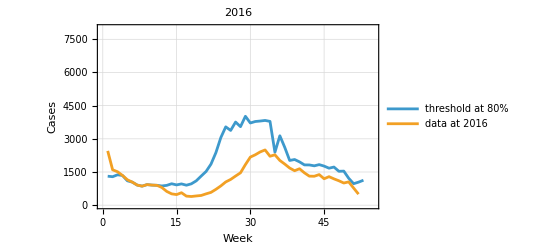
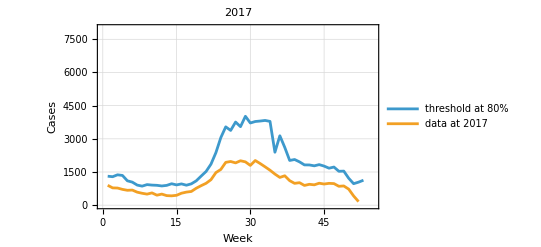
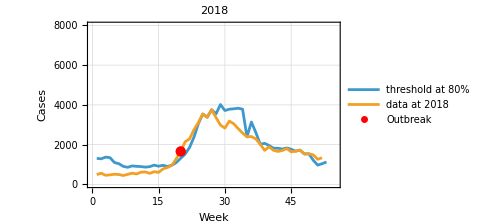
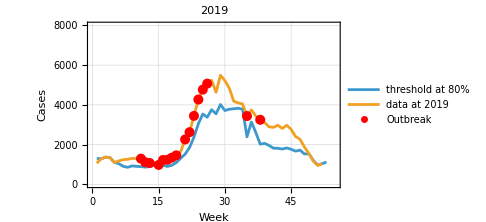
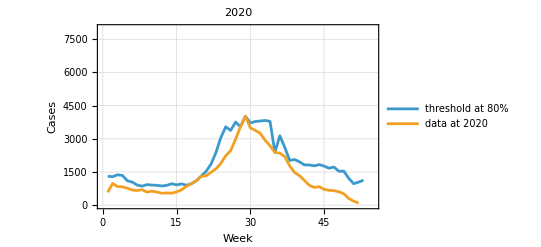
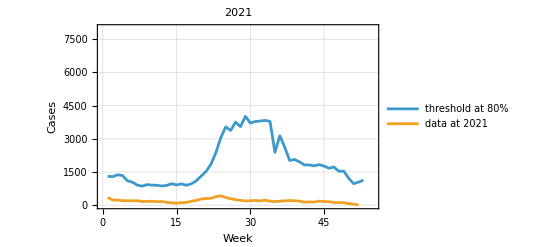
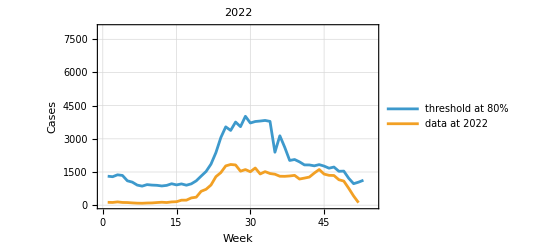
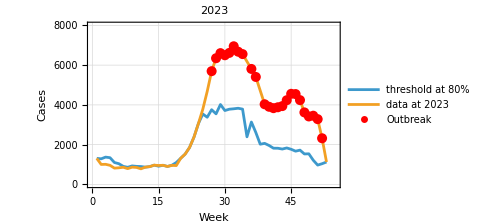

```mathematica
FindOutBreak/@Range[2016,2024]
```

```mathematica
(* episode years = {2019, 2023, 2024} *)
outbreak80=Table[
trsh=Select[Normal@Select[ab80,#year==yr&][All,{#week,#cases,#above}&],#[[3]]==True&][[All,{1,2}]];
trshass=Association[#1->#2&@@@trsh];
runs=Select[Split[trsh[[All,1]],#2==#1+1&],Length[#]>=2&];
intervals={First[#],Last[#]}&/@runs;
lengths=Length/@runs;
Flatten[Thread[{#,Lookup[trshass,#]}]&/@runs,1],
{yr,{2019,2023,2024}}
]
```

{{{11,1296},{12,1115},{13,1075},{15,980},{16,1228},{17,1237},{18,1348},{19,1462},{21,2262},{22,2627},{23,3447},{24,4271},{25,4769},{26,5070}},{{27,5697},{28,6348},{29,6604},{30,6497},{31,6616},{32,6949},{33,6676},{34,6556},{36,5809},{37,5406},{39,4032},{40,3906},{41,3836},{42,3881},{43,3940},{44,4235},{45,4557},{46,4545},{47,4240},{48,3622},{49,3419},{50,3456},{51,3283},{52,2321}},{{1,2733},{2,3422},{3,2936},{4,2349},{5,1985},{6,1894},{7,1791},{8,1517},{9,1535},{10,1422}}}

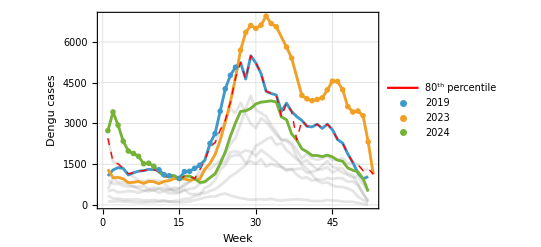

```mathematica
Show[
ListPlot[byYW[#][All,1]&/@{1,2,3,4,5,6,7,8,9},Joined->True,Frame->True,FrameLabel->{"Week", "Dengu cases"},GridLines->Automatic,PlotStyle->Opacity[0.2,Gray],LabelStyle->Directive[Bold, Medium,FontFamily->"Times New Roman"]],
ListPlot[byYW[#][All,1]&/@{4,8,9},Joined->True],
ListPlot[thresholdByWeek[[3]],Joined->True,PlotStyle->{Red,Thick,Dashed},PlotLegends->LineLegend[{Red},{"80^th percentile"}]],
ListPlot[outbreak80,PlotLegends->{"2019","2023","2024"},PlotMarkers->"OpenMarkers"]
]
```

```mathematica
Clear[consecutiveIntervals];
consecutiveIntervals[trshlist_,minLen_:2]:=Module[{runs,list,assc,tot,max,t2peak},
assc=(#1->#2&@@@trshlist)//Association;
list=trshlist[[All,1]];
runs=Select[Split[list,#2==#1+1&],Length[#]>=minLen&];
tot=Total/@(Lookup[assc,#]&/@runs);
max=Max/@(Lookup[assc,#]&/@runs);
t2peak=PositionLargest/@(Lookup[assc,#]&/@runs)-1;
<|"Intervals"->({First[#],Last[#]}&/@runs),"Lengths"->(Length/@runs),"total"->tot,"Maximum"->max,"Time2Peak"->t2peak|>]
```

```mathematica
ExtractInfo[Y_Integer]:=Module[{trsh},
trsh=Select[Normal@Select[ab80,#year==Y&][All,{#week,#cases,#above}&],#[[3]]==True&][[All,{1,2}]];
consecutiveIntervals[trsh]
];
```

```mathematica
Dataset@Association@Table[y->ExtractInfo[y],{y,2016,2024}]
```

```mathematica
epi=
```

```mathematica
ShortenByK[ds_Dataset,k_Integer?NonNegative]:=ds[All,Function[row,Module[{d=row["duration"],tc=row["total_cases"],d2,tc2},d2=Max[1,d-k];
tc2=tc*(d2/d);
(*proportional reduction*)
Join[row,<|"cf_duration"->d2,"cf_total_cases"->tc2,"cases_averted"->(tc-tc2),"pct_averted"->100.0*(tc-tc2)/tc|>]]]];
```

```mathematica
(*k = 1 week*)
short1=ShortenByK[epi,1]
```

```mathematica
(* k= 2 weeks*)
short2=ShortenByK[epi, 2]
```

```mathematica
(* k = 3 weeks *)
short3=ShortenByK[epi,3]
```

```mathematica
(* k = 4 weeks*)
short4=ShortenByK[epi,4]
```

```mathematica
iqr=N@Normal@Quantile[#[All,#"cases_averted"&],{0.25,0.5,0.75}]&/@{short1,short2,short3,short4}
```

{{1251.,3741.,5607.5},{2502.,5607.5,7610.43},{3753.,6475.2,11415.6},{5004.,8633.6,15220.9}}

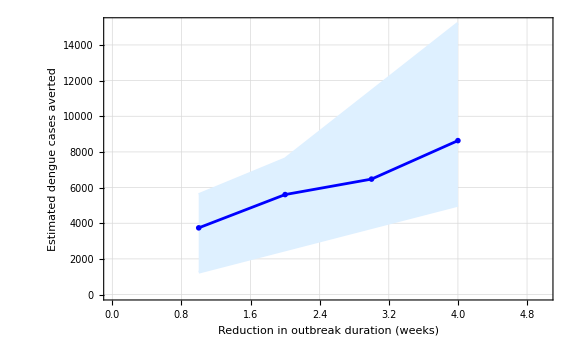

```mathematica
ListPlot[{iqr[[All,2]],iqr[[All,1]],iqr[[All,3]]},Joined->{True,True,True},Frame->True,GridLines->Automatic,PlotRange->{{0,5},{0,Automatic}},PlotMarkers->{"OpenMarkers",None,None},PlotStyle->{Blue,LightBlue,LightBlue},Filling->{2->{3}},FillingStyle->LightBlue,FrameLabel->{"Reduction in outbreak duration (weeks)", "Estimated dengue cases averted"},LabelStyle->Directive[Bold, Medium,FontFamily->"Times New Roman"],ImageSize->Large]
```

```mathematica
targetQ=0.25;
targetDur=Quantile[Normal[epi[All,"duration"]],targetQ];

ShortenToTarget[ds_Dataset,target_Integer?Positive]:=ds[All,Function[row,Module[{d=row["duration"],tc=row["total_cases"],d2,tc2},d2=Min[d,target];(*only shorten,never lengthen*)
tc2=tc*(d2/d);
Join[row,<|"cf_duration"->d2,"cf_total_cases"->tc2,"cases_averted"->(tc-tc2),"pct_averted"->100.0*(tc-tc2)/tc|>]]]];

cfTarget=ShortenToTarget[epi,Round[targetDur]];
cfTarget
```

```mathematica
BootstrapAverted[ds_Dataset,makeCF_,n_Integer:5000]:=Module[{rows=Normal[ds],m=Length[Normal[ds]],totals},totals=Table[Module[{sample,cf},sample=RandomChoice[rows,m];(*resample rows with replacement*)
cf=makeCF[Dataset[sample]];
Total[Normal[cf[All,"cases_averted"]]]],{n}];
<|"mean_averted"->Mean[totals],"median_averted"->Median[totals],"CI95"->Quantile[totals,{0.025,0.975}]|>];
```

```mathematica
(*shorten by 2 weeks*)
BootstrapAverted[epi,(ShortenByK[#,2]&),5000]//N
```

<|mean_averted→42872.7,median_averted→42700.1,CI95→{26830.7,61085.8}|>

```mathematica
(* shorten to 25% Quartile*)
BootstrapAverted[epi,(ShortenToTarget[#,Round[targetDur]]&),5000]//N
```

<|mean_averted→102402.,median_averted→100654.,CI95→{31335.8,188254.}|>